```mathematica
f[x_, y_] := x^2 + y^2
```

{2 x,2 y}

{4 Cos[x] (Cos[x]^2+Cos[y]^2) Sin[x],4 Cos[y] (Cos[x]^2+Cos[y]^2) Sin[y]}

-Graphics3D-

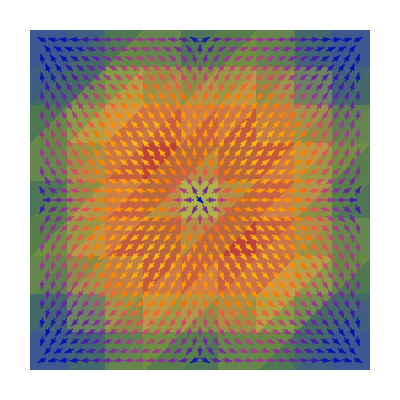

```mathematica
g[x_, y_] := -(Cos[x]^2+Cos[y]^2)^2

Grad[f[x,y], {x, y}]
grad = Grad[g[x,y], {x, y}]

potential =
Plot3D[g[x, y], {x, -Pi/2, Pi/2}, {y, -Pi/2, Pi/2},
ColorFunction->"DarkRainbow", PlotStyle->Opacity[0.8]]

gradient =
VectorDensityPlot[{grad}, {x, -Pi/2, Pi/2}, {y, -Pi/2, Pi/2},
Frame->False,PlotRangePadding->None,ColorFunction->"DarkRainbow",VectorPoints->30]
```

```mathematica
texture = Graphics3D[{Texture[gradient],Polygon[{{-Pi/2,-Pi/2,-4},{Pi/2,-Pi/2,-4},{Pi/2,Pi/2,-4},{-Pi/2,Pi/2,-4}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Show[potential, texture]
```

-Graphics3D-